```mathematica
Quit[]
```

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
RinfC[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - -I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[I k r]Hypergeometric1F1[-I/(k a0)+l+1,2l+2,- 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
Integrate[Rb[2,1,r]^2 r^2,{r,0,Infinity}]
```

ConditionalExpression[1, Re[a0]>0]

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^4(2l-3n + 1)/(l+1/2));
```

## 322 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.13451×10^-8 λ^2 μ^2 α^4+O[α]^6

## 322 x 411 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->8,AccuracyGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.73534×10^-9 λ^2 μ^2 α^4+O[α]^6

## 411 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.23477×10^-9 λ^2 μ^2 α^4+O[α]^6

## 422 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.61941×10^-8 λ^2 μ^2 α^4+O[α]^6

## 433 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.20827×10^-11 λ^2 μ^2 α^4+O[α]^6

## 322 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.61936×10^-9 λ^2 μ^2 α^4+O[α]^6

## 211 x 211 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];

val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.6113×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

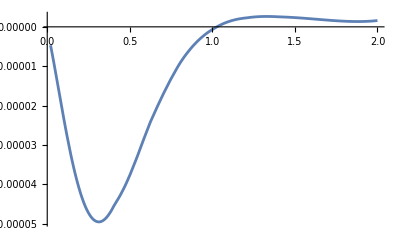

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 211 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.25146×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

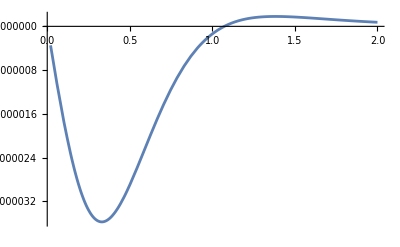

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.38719×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.52885×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 411 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

1

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.67451×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

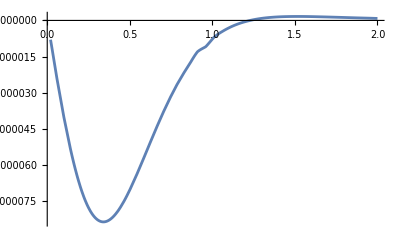

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

9.23046×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.45527×10^-8 λ^2 μ α^7+O[α]^10

## 411 x 411 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.02759×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

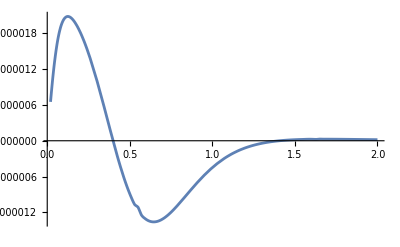

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.19501×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.47414×10^-11 λ^2 μ α^7+O[α]^10

## 211 x 322 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

9.98537×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

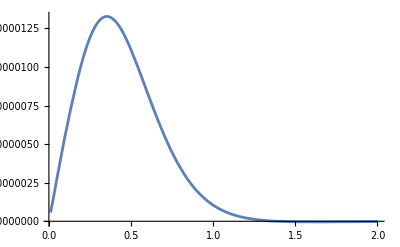

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.21466×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.067×10^-8 λ^2 μ α^7+O[α]^10

## 322 x 322 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.90982×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

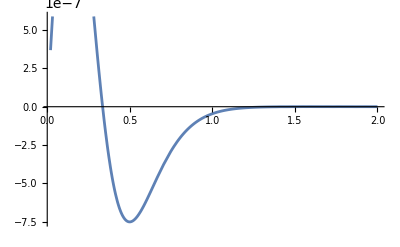

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.86687×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92465×10^-9 λ^2 μ α^7+O[α]^10

## 211 x 422 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.82881×10^-11 λ^2 μ α^3-1.79057×10^-10 (λ^2 μ) α^5+1.02383×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->8,AccuracyGoal->8];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

$Aborted

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

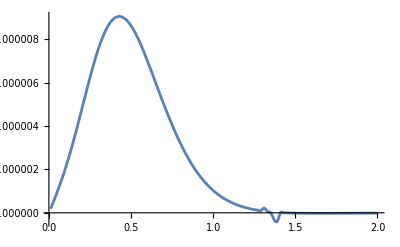

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.03201×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

7.82881×10^-11 λ^2 μ α^3+6.1081×10^-13 λ^2 μ α^5+1.1899×10^-13 λ^2 μ α^7+O[α]^8

## 411 x 411 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.19286×10^-11 λ^2 μ α^3-2.24759×10^-10 (λ^2 μ) α^5+5.75922×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

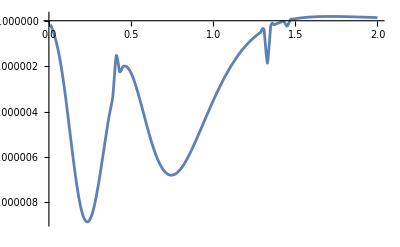

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.16422×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.19286×10^-11 λ^2 μ α^3-1.23712×10^-10 (λ^2 μ) α^5+1.74495×10^-10 λ^2 μ α^7+O[α]^8